```mathematica
IONS={"06+","07+","08+","09+","10+","11+","12+","13+","14+"};
ZO=<|"06+"->0,"07+"->1,"08+"->2,"09+"->3,"10+"->4,"11+"->5,"12+"->6,"13+"->7,"14+"->8|>;
<<"AMBiT`";
<<"ReadAMBiTOutput`";
eV=27.211;
(*Turn off Fit Errors*)
Off[FindFit::cvmit]
Off[NonlinearModelFit::cvmit]
Off[Power::infy]
```

## Image Properties

```mathematica
FS=14; FF="Helvetica"; (* Plotting Font Size and Font*)
ImRes=600; (* Export Image Resolution dpi *)
```

```mathematica
filename="C:\\Users\\mattb\\Documents\\Mathematica\\Try_3\\LevelDensity\\Sn07+_00.CS.txt";
file=Import[filename,"CSV"];
{Shells,Energy,Num}=ReadLevels[file];
```

```mathematica
filename2="\\Data\\Excel_All_MBQC\\Sn13+Data.xlsx"
filename2="C:\\Users\\mattb\\Documents\\Mathematica\\GitHub_Repository\\Data\\Excel_All_MBQC\\Sn13+Data.xlsx"
Spreading=Import[filename2,{"Data",1}];
```

\Data\Excel_All_MBQC\Sn13+Data.xlsx

C:\Users\mattb\Documents\Mathematica\GitHub_Repository\Data\Excel_All_MBQC\Sn13+Data.xlsx

{Source.Name,J Pi,L,Hij0,V,D_WD,dD_WD,V/D,G,dG,Text Between Delimiters,Gap}

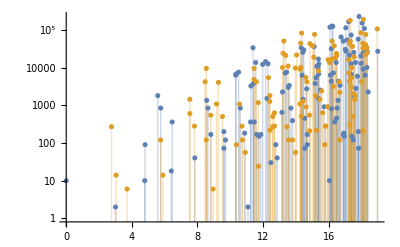

```mathematica
Levels=Import[FILE,{"Data",2}];
Shell=Levelsᵀ[[1]][[2;;-1]];
Num=Levelsᵀ[[2]][[2;;-1]];
Energy=Levelsᵀ[[3]][[2;;-1]];
Energy=Energy-Min[Energy];
Energy=Energy eV;
L=Length[Energy];
Odd=ConstantArray[False,L];
Even=ConstantArray[True,L];

For[i=1,i≤L,i++,{
S=Shell[[i]];
(*Print[S];*)
S1=Characters[S];
x=StringPosition[S,"p"];
y=StringPosition[S,"f"];
(*Print[x];
Print[y];*)
a=0;
b=0;
For[j=1,j≤Length[x],j++,{
a=a+ToExpression[S1[[x[[j]][[1]]+1]]];
}];
For[j=1,j≤Length[y],j++,{
b=b+ToExpression[S1[[y[[j]][[1]]+1]]];
}];
(*Print[a];
Print[b];*)
If[OddQ[a+b]==True, 
Odd[[i]]=True
];
Even[[i]]=Not[Odd[[i]]];
}]

EEven=Pick[Energy,Even];
OrdE=Ordering[EEven];
EEven=EEven[[OrdE]];
NEven=Pick[Num,Even];
NEven=NEven[[OrdE]];
CNEven=Accumulate[NEven];

EOdd=Pick[Energy,Odd];
OrdO=Ordering[EOdd];
EOdd=EOdd[[OrdO]];
NOdd=Pick[Num,Odd];
NOdd=NOdd[[OrdO]];
CNOdd=Accumulate[NOdd];

im1=ListLogPlot[{{EEven/eV,NEven}ᵀ,{EOdd/eV,NOdd}ᵀ},Filling->Axis]
```

```mathematica
z=Range[0,25 eV,0.01]
Zo=ConstantArray[0,Length[z]];
Ze=ConstantArray[0,Length[z]];
G=22;
g=G/2;
For[i=1,i≤L,i++,{
If[Even[[i]]==True,{
De=1/(π g)g^2/(g^2+(z-Energy[[i]])^2)Num[[i]];
Ze=Ze+De;},{
D1o=1/(π g)g^2/(g^2+(z-Energy[[i]])^2)Num[[i]];
Zo=Zo+D1o;}]
}]
Z=Ze+Zo;
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,67984,680.06,680.07,680.08,680.09,680.1,680.11,680.12,680.13,680.14,680.15,680.16,680.17,680.18,680.19,680.2,680.21,680.22,680.23,680.24,680.25,680.26,680.27}
 |  |  |  |

-Graphics-

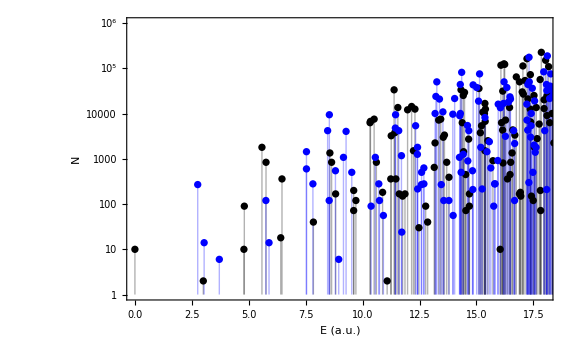

```mathematica
imN1=ListLogPlot[{{z/eV,Ze}ᵀ,{z/eV,Zo}ᵀ,{z/eV,Z}ᵀ},Joined->True,PlotRange->{{0,18},{1,10^6}},ImageSize->Large,Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"E (a.u)","N"},PlotStyle->{Black,Blue,Orange},FrameTicks->{Automatic,Table[{10^k,Superscript[10,k]},{k,0,6}]},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],GridLines->{None,Full}]
imN2=ListLogPlot[{{EEven/eV,NEven}ᵀ,{EOdd/eV,NOdd}ᵀ},Filling->Axis,PlotRange->{{0,18},{1,10^6}},ImageSize->Large,Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"E (a.u.)","N"},PlotStyle->{Black,Blue,Orange},FrameTicks->{Automatic,Table[{10^k,Superscript[10,k]},{k,0,6}]},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],GridLines->{None,Full}]
```

```mathematica
Export["C:/Users/mattb/Documents/Mathematica/Try_3/LevelDensity/Sn13Ncont.eps",imN1,ImageResolution->ImRes]
Export["C:/Users/mattb/Documents/Mathematica/Try_3/LevelDensity/Sn13Ndiscrete.eps",imN2,ImageResolution->ImRes]
```

C:/Users/mattb/Documents/Mathematica/Try_3/LevelDensity/Sn13Ncont.eps

C:/Users/mattb/Documents/Mathematica/Try_3/LevelDensity/Sn13Ndiscrete.eps

```mathematica
J="1";
JPI=Spreadingᵀ[[2]][[2;;-1]];
LJ=Length[JPI];
Feven=StringPosition[JPI,J<>"e"];
Fodd=StringPosition[JPI,J<>"o"];

EJmask=ConstantArray[False,LJ];
OJmask=ConstantArray[False,LJ];
For[i=1,i≤LJ,i++,{
If[Length[Feven[[i]]]≠0 && Feven[[i]][[1]][[1]]==1,EJmask[[i]]=True]
}];
For[i=1,i≤LJ,i++,{
If[Length[Fodd[[i]]]≠0 && Fodd[[i]][[1]][[1]]==1,OJmask[[i]]=True]
}];

Gspr=Spreadingᵀ[[9]][[2;;-1]];
dGspr=Spreadingᵀ[[10]][[2;;-1]];
Gap=Spreadingᵀ[[11]][[2;;-1]];

Eeven=Pick[Gap,EJmask];
OrdEJ=Ordering[Eeven];
Eeven=Eeven[[OrdEJ]];
EGspr=Pick[Gspr,EJmask];
EGspr=EGspr[[OrdEJ]];
EdGspr=Pick[dGspr,EJmask];
EdGspr=EdGspr[[OrdEJ]];

Eodd=Pick[Gap,OJmask];
OrdOJ=Ordering[Eodd];
Eodd=Eeven[[OrdOJ]];
OGspr=Pick[Gspr,OJmask];
OGspr=OGspr[[OrdOJ]];
OdGspr=Pick[dGspr,OJmask];
OdGspr=OdGspr[[OrdOJ]];

excludeE=8;
EGspr=EGspr[[excludeE;;-1]];
EdGspr=EdGspr[[excludeE;;-1]];
Eeven=Eeven[[excludeE;;-1]];


excludeO=30;
OGspr=OGspr[[excludeO;;-1]];
OdGspr=OdGspr[[excludeO;;-1]];
Eodd=Eodd[[excludeO;;-1]];
```

```mathematica
Ce=Accumulate[Ze];
Co=Accumulate[Zo];
Ct=Accumulate[Z];
ListLogPlot[{{z/eV,Ce}ᵀ,{z/eV,Co}ᵀ,{z/eV,Ct}ᵀ},Joined->True,PlotRange->{{0,20},{1,10^9}},ImageSize->Large,Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"Level Spacing (eV)","Probability"},PlotStyle->{Black,Blue,Orange},FrameTicks->{Automatic,Table[{10^k,Superscript[10,k]},{k,0,9}]},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],GridLines->{Automatic,Full}]
```

-Graphics-

```mathematica
dataE=Partition[Riffle[z/eV,Ce],2];
dataE=Select[dataE,8<#[[1]]<15&];
fitparamsE=NonlinearModelFit[dataE,A1 Exp[A2 X],{{A1,10^8},{A2,0.5}},X];
(*fitparams=NonlinearModelFit[data,2/(π Γ)(Γ^2/4)/((Ec-x)^2+Γ^2/4),{{Ec,Em},{Γ,0.5}},x];*)
fitvalE=fitparamsE["BestFitParameters"];
RMSE=RootMeanSquare[fitparamsE["FitResiduals"]];
R2E=fitparamsE["RSquared"];

CFitE=A1 Exp[A2 z/eV]/.fitvalE;

dataO=Partition[Riffle[z/eV,Co],2];
dataO=Select[dataO,5≤ #[[1]]≤ 17&];
fitparamsO=NonlinearModelFit[dataO,A1 Exp[A2 X],{{A1,10^8},{A2,0.5}},X];
(*fitparams=NonlinearModelFit[data,2/(π Γ)(Γ^2/4)/((Ec-x)^2+Γ^2/4),{{Ec,Em},{Γ,0.5}},x];*)
fitvalO=fitparamsO["BestFitParameters"];
RMSO=RootMeanSquare[fitparamsO["FitResiduals"]];
R2O=fitparamsE["RSquared"];

CFitO=A1 Exp[A2 z/eV]/.fitvalO;



ListLogPlot[{{z/eV,Ce}ᵀ,{z/eV,Co}ᵀ,{z/eV,Ct}ᵀ,{z/eV,CFitE}ᵀ,{z/eV,CFitO}ᵀ},Joined->True,PlotRange->{{0,20},{1,10^9}},ImageSize->Large,Frame->{True,True,False,False},PlotRangePadding->0,FrameLabel->{"Level Spacing (eV)","Probability"},PlotStyle->{Black,Blue,Orange,Red,Purple},FrameTicks->{Automatic,Table[{10^k,Superscript[10,k]},{k,0,9}]},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],GridLines->{Automatic,Full}]
```

-Graphics-

```mathematica
fitvalO
```

{A1→109088.,A2→0.385431}

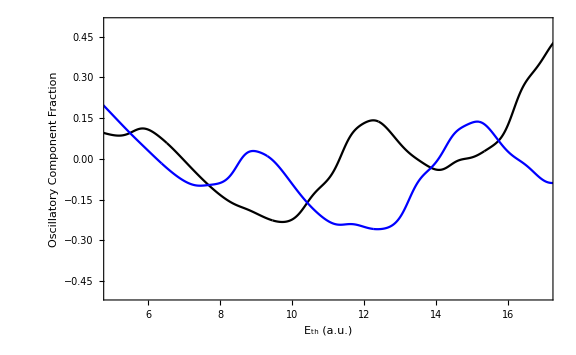
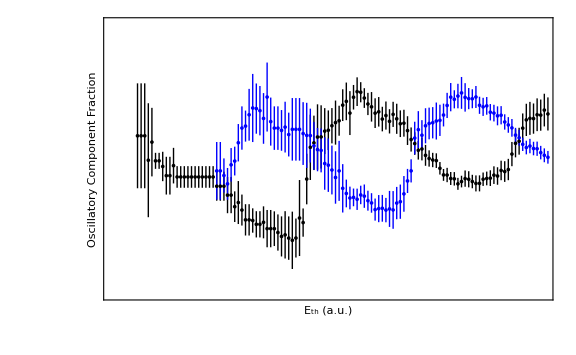

```mathematica
OscE=(Ce-CFitE)/CFitE;
OscO=(Co-CFitO)/CFitO;

P1=ListLinePlot[{{z/eV,OscE}ᵀ,{z/eV,OscO}ᵀ},ImageSize->Large,PlotRange->{{5,17},{-0.5,0.5}},Frame->{True,True,True,False},FrameLabel->{{"Oscillatory Component Fraction","Γ_spr (eV)"},{"E_th (a.u.)",None}},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],ImagePadding->60,PlotStyle->{Black,Blue}];
P2=ListPlot[{{Eeven,Table[Around[EGspr[[n]],EdGspr[[n]]],{n,1,Length[EGspr]}]}ᵀ,{Eodd,Table[Around[OGspr[[n]],OdGspr[[n]]],{n,1,Length[OGspr]}]}ᵀ},ImageSize->Large, Frame->{False,False,False,True},Axes->False,FrameTicks->{{None,All},{None,None}},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF],PlotRange->{{5,17},{0,40}},IntervalMarkers->"Fences",FrameLabel->{{"Oscillatory Component Fraction","Γ_spr (eV)"},{"E_th (a.u.)",None}},PlotStyle->{Black,Blue},ImagePadding->60];
Ov=Overlay[{P1,P2}]
```

```mathematica
Export["C:/Users/mattb/Documents/Mathematica/Try_3/LevelDensity/Sn13J1oOsc.eps",Ov,ImageResolution->ImRes]
```

C:/Users/mattb/Documents/Mathematica/Try_3/LevelDensity/Sn13J1oOsc.eps

230

{A3→0.0163087,A4→3.27215}

0.999506

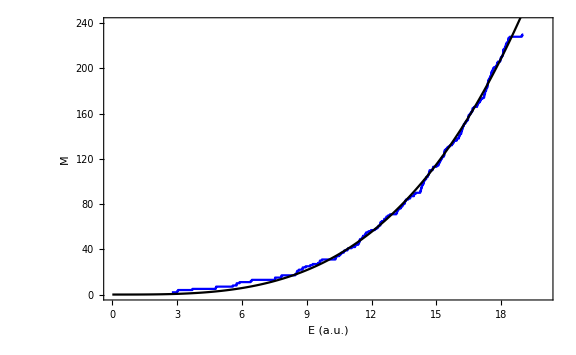

```mathematica
LE=Length[Energy]
config=Range[2,LE,1];
En=Sort[Energy]/eV;
En=En[[2;;-1]];
ListPlot[{En,config}ᵀ];
dataC=Partition[Riffle[En,config],2];
(*dataC=Select[dataC,8<#[[1]]<15&];*)
fitparamsC=NonlinearModelFit[dataC,A3 var^A4,{{A3,0.001},{A4,3}},var];
(*fitparams=NonlinearModelFit[data,2/(π Γ)(Γ^2/4)/((Ec-x)^2+Γ^2/4),{{Ec,Em},{Γ,0.5}},x];*)
fitvalC=fitparamsC["BestFitParameters"]
RMSC=RootMeanSquare[fitparamsC["FitResiduals"]];
R2C=fitparamsC["RSquared"]
Y=Range[0,20,0.1];
M=A3 Y^A4/.fitvalC;
im6=ListLinePlot[{Y,M}ᵀ,PlotStyle->Black];
im7=ListStepPlot[{En,config}ᵀ,PlotStyle->Blue];
S2=Show[{im7,im6},ImageSize->Large,Frame->{True,True,False,False},PlotRangePadding->0,PlotRange->{{0,20},{0,240}},FrameLabel->{"E (a.u.)","M"},LabelStyle->Directive[Black,FontSize->FS,FontFamily->FF]]
```

```mathematica
Export["C:/Users/mattb/Documents/Mathematica/Try_3/LevelDensity/Sn13M.eps",S2,ImageResolution->ImRes]
```

C:/Users/mattb/Documents/Mathematica/Try_3/LevelDensity/Sn13M.eps